# Paso I. Variables.

```mathematica
NPart = 20; (*Número de pasos*)
init=1;end = NPart+1;
```

```mathematica
sxVar = Table[sx[i], {i, init, end}]; (*Posición en eje 0X*)
syVar = Table[sy[i], {i, init, end}]; (*Posición en eje 0Y*)
vxVar = Table[vx[i],{i, init, end}]; (*Velocidad en eje 0X*)
```

```mathematica
vyVar = Table[vy[i], {i, init, end}]; (*Velocidad en eje 0Y*)
```

```mathematica
ΛxVar = Table[Λx[i], {i, init, end}]; (*Aceleración artificial en el eje 0X*)
ΛyVar = Table[Λy[i], {i, init, end}]; (*Aceleración artificial en el eje 0Y*)
```

```mathematica
Vars = Join[sxVar, syVar, vxVar, vyVar, ΛxVar, ΛyVar];
```

# Paso II. Parámetros

```mathematica
(*Constante de gravitación universal*)
G=1;
(*Radio de la Tierra*)
roE=2;
(*Radio de la Luna*)
roM=1;
(*Masa de la Tierra*)
mE=10;
(*Masa de la Luna*)
mM=1;
(*Distancia entre el centro de la Tierra y el centro de la Luna*)
a = 20;
(*Vector apunta Tierra*)
rE={0,0};
(*Vector apunta Luna*)
rM={a,0};
(*Ángulo Salida*)
tethaM = Pi/2;
(*Ángulo Llegada*)
tethaE = 3 Pi /2;
(*Duración de la trayectoria del vuelo*)
TTT = 14*24*60*60;
TT = 1000;
T=1;
(*Partición del tiempo*)
h=T/NPart;
(*Vector direccional cohete*)
(*rR[t_]:={sx[t],sy[t]}/Sqrt[sx[t]^2+sy[t]^2];*)(*Como función*)
(*Componente apunta cohete en OX*)
rRx = Table[sxVar[[k]]/Sqrt[sxVar[[k]]^2 + syVar[[k]]^2], {k, 1, NPart+1}];
(*Componente direccional cohete en OY*)
rRy = Table[syVar[[k]]/Sqrt[sxVar[[k]]^2 + syVar[[k]]^2], {k, 1, NPart+1}];
(*Distancia Cohete-Tierra*)
dER=Table[Sqrt[sxVar[[k]]^2+syVar[[k]]^2], {k, 1, NPart+1}];
(*Distancia Cohete-Luna*)
dMR=Table[Sqrt[(sxVar[[k]]-a)^2+syVar[[k]]^2], {k, 1, NPart+1}];
(*Componentes direccionales vector Cohete-Luna*)
```

```mathematica
rMRx= Table[(sxVar[[k]]-rM[[1]])/Norm[{sxVar[[k]], syVar[[k]]}-rM, 2], {k, 1, NPart+1}];
rMRy= Table[(syVar[[k]]-rM[[2]])/Norm[{sxVar[[k]], syVar[[k]]}-rM, 2], {k, 1, NPart+1}];
(*Componentes direccionales vector Cohete-Tierra*)
rERx= Table[(sxVar[[k]]-rE[[1]])/Norm[{sxVar[[k]], syVar[[k]]}-rE, 2], {k, 1, NPart+1}];
rERy= Table[(sxVar[[k]]-rE[[2]])/Norm[{sxVar[[k]], syVar[[k]]}-rE, 2], {k, 1, NPart+1}];
```

# Paso III. Restricciones Igualdades. Condiciones Iniciales.

```mathematica
(*3.- Valores iniciales*)
(*Posiciones de salida del cohete*)
sInit = {sxVar[[1]]==    roE*Cos[tethaE], syVar[[1]]==    roE*Sin[tethaE]};
(*--------------------*)
(*Posiciones de llegada del cohete*)
sFinal = {sxVar[[NPart+1]]==   a+ roM*Cos[tethaM], syVar[[NPart+1]]==    roM*Sin[tethaM]};
(*--------------------*)
(*Velocidad de salida*)
v0 =50; (*m/s*)
vInit = {vxVar[[1]]==    v0*Cos[tethaE], vyVar[[1]]==    v0*Sin[tethaE]};
(*--------------------*)
(*Velocidad de llegada*)
vN = 0; (*m/s*)
vFinal = {vxVar[[NPart+1]]==    vN*Cos[tethaM], vyVar[[NPart+1]]==    vN*Sin[tethaM]}

(*----------------------------------*)
(*Aceleración de salida y llegada*)
```

{vx[21]==0,vy[21]==0}

```mathematica
RInit = Join[sInit, sFinal, vInit, vFinal]
```

{sx[1]==0,sy[1]==-2,sx[21]==20,sy[21]==1,vx[1]==0,vy[1]==-50,vx[21]==0,vy[21]==0}

# Paso IV. Restricciones Desigualdad.

```mathematica
(*Evitar la colisión con la Tierra*)
R1= Table[sxVar[[k]]^2+syVar[[k]]^2≥ roE^2 ,{k,1,NPart+1}];
(* Evitar la conlisión con la Luna*)
R2=Table[(sxVar[[k]]-a)^2+syVar[[k]]^2≥ roM^2,{k,1,NPart+1}];
(*----------------------------------*)
(*Primero discretizamos el tiempo y aplicamos el Método Euler Explícito*)
Gx=Table[-((N[mM G]/dMR[[k]]^2)*rMRx[[k]]+(N[mE G]/dER[[k]]^2)*rERx[[k]]), {k, 1, NPart+1}];(*Parte de la expresión final*)
R3=Table[vxVar[[k+1]]==   (Gx[[k]]+ΛxVar[[k]])*h+vxVar[[k]],{k,1,NPart}];
Gy=Table[-((N[mM G]/dMR[[k]]^2)*rMRy[[k]]+(N[mE G]/dER[[k]]^2)*rERy[[k]]), {k, 1, NPart+1}];
R4=Table[vyVar[[k+1]]==   (Gy[[k]]+ΛyVar[[k]])*h+vyVar[[k]],{k,1,NPart}];
```

```mathematica
R5 = Table[sxVar[[k+1]]== vxVar[[k]]*h+sxVar[[k]], {k, 1, NPart}];
R6 = Table[syVar[[k+1]]== vyVar[[k]]*h+syVar[[k]], {k, 1, NPart}];
R71 = Table[ΛxVar[[k]]≥ -10, {k, 1, NPart+1}];
R72 = Table[ΛxVar[[k]]≤  10, {k, 1, NPart+1}];
R81 = Table[ΛyVar[[k]]≥ -10, {k, 1, NPart+1}];
R82 = Table[ΛyVar[[k]]≤  10, {k, 1, NPart+1}];
```

```mathematica
restrictions = Join[ R3, R4,R5, R6, R71, R72, R81, R82 ,  RInit];
```

# Paso V. Función Objetivo.

```mathematica
(*5) Función Objetivo*)
(*------------------------------------------------------------------------------------*)
Objetive=Sum[Λx[tn]^2+Λy[tn]^2,{tn,1,NPart+1}];
(*Restricciones*)

SolAlt = FindMinimum[{Objetive, restrictions},Vars]
```

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 500 iterations.

{193.765,{sx[1]→0.,sx[2]→0.,sx[3]→0.431779,sx[4]→1.24135,sx[5]→2.27125,sx[6]→3.46389,sx[7]→4.77164,sx[8]→6.15495,sx[9]→7.5807,sx[10]→9.02094,sx[11]→10.4517,sx[12]→11.8518,sx[13]→13.2023,sx[14]→14.4855,sx[15]→15.684,sx[16]→16.7803,sx[17]→17.756,sx[18]→18.5906,sx[19]→19.2612,sx[20]→19.7414,sx[21]→20.,sy[1]→-2.,sy[2]→-4.5,sy[3]→-6.24888,sy[4]→-7.34619,sy[5]→-7.98706,sy[6]→-8.25989,sy[7]→-8.23729,sy[8]→-7.97889,sy[9]→-7.53374,sy[10]→-6.94245,sy[11]→-6.23907,sy[12]→-5.45283,sy[13]→-4.60964,sy[14]→-3.73364,sy[15]→-2.84859,sy[16]→-1.97927,sy[17]→-1.15297,sy[18]→-0.400996,sy[19]→0.239691,sy[20]→0.724663,sy[21]→1.,vx[1]→0.,vx[2]→8.63558,vx[3]→16.1915,vx[4]→20.5979,vx[5]→23.8528,vx[6]→26.1551,vx[7]→27.666,vx[8]→28.5151,vx[9]→28.8048,vx[10]→28.6142,vx[11]→28.0024,vx[12]→27.0105,vx[13]→25.6633,vx[14]→23.9705,vx[15]→21.927,vx[16]→19.5128,vx[17]→16.6922,vx[18]→13.4129,vx[19]→9.60366,vx[20]→5.17179,vx[21]→0.,vy[1]→-50.,vy[2]→-34.9776,vy[3]→-21.9462,vy[4]→-12.8174,vy[5]→-5.45657,vy[6]→0.451965,vy[7]→5.16803,vy[8]→8.90304,vy[9]→11.8258,vy[10]→14.0675,vy[11]→15.7249,vy[12]→16.8637,vy[13]→17.5199,vy[14]→17.7011,vy[15]→17.3864,vy[16]→16.526,vy[17]→15.0395,vy[18]→12.8137,vy[19]→9.69943,vy[20]→5.50674,vy[21]→0.,Λx[1]→2.27061,Λx[2]→2.27061,Λx[3]→2.27061,Λx[4]→2.27061,Λx[5]→2.27061,Λx[6]→2.27061,Λx[7]→2.27061,Λx[8]→2.27061,Λx[9]→2.27061,Λx[10]→2.27061,Λx[11]→0.0444109,Λx[12]→-1.73295,Λx[13]→-2.27061,Λx[14]→-2.27061,Λx[15]→-2.27061,Λx[16]→-2.27061,Λx[17]→-2.27061,Λx[18]→-2.27061,Λx[19]→-2.27061,Λx[20]→-2.27061,Λx[21]→-0.0000313463,Λy[1]→2.27061,Λy[2]→2.27061,Λy[3]→2.27061,Λy[4]→2.27061,Λy[5]→2.27061,Λy[6]→2.27061,Λy[7]→2.27061,Λy[8]→2.27061,Λy[9]→2.27061,Λy[10]→2.27061,Λy[11]→2.27061,Λy[12]→2.27061,Λy[13]→2.27061,Λy[14]→-0.00984392,Λy[15]→-2.27061,Λy[16]→-2.27061,Λy[17]→-2.27061,Λy[18]→-2.27061,Λy[19]→-2.27061,Λy[20]→-2.27061,Λy[21]→-0.0000313463}}

```mathematica
Plots = Table[{SolAlt[[2, k, 2]], SolAlt[[2, k+NPart+1, 2]]}, {k, 1, NPart+1}]
```

{{0.,-2.},{0.,-4.5},{0.431779,-6.24888},{1.24135,-7.34619},{2.27125,-7.98706},{3.46389,-8.25989},{4.77164,-8.23729},{6.15495,-7.97889},{7.5807,-7.53374},{9.02094,-6.94245},{10.4517,-6.23907},{11.8518,-5.45283},{13.2023,-4.60964},{14.4855,-3.73364},{15.684,-2.84859},{16.7803,-1.97927},{17.756,-1.15297},{18.5906,-0.400996},{19.2612,0.239691},{19.7414,0.724663},{20.,1.}}

```mathematica
A = ListLinePlot[Plots, PlotStyle->PointSize[Large]];
```

```mathematica
B =Graphics[Circle[{0, 0}, roE]];
CC =Graphics[Circle[{a, 0}, roM]];
```

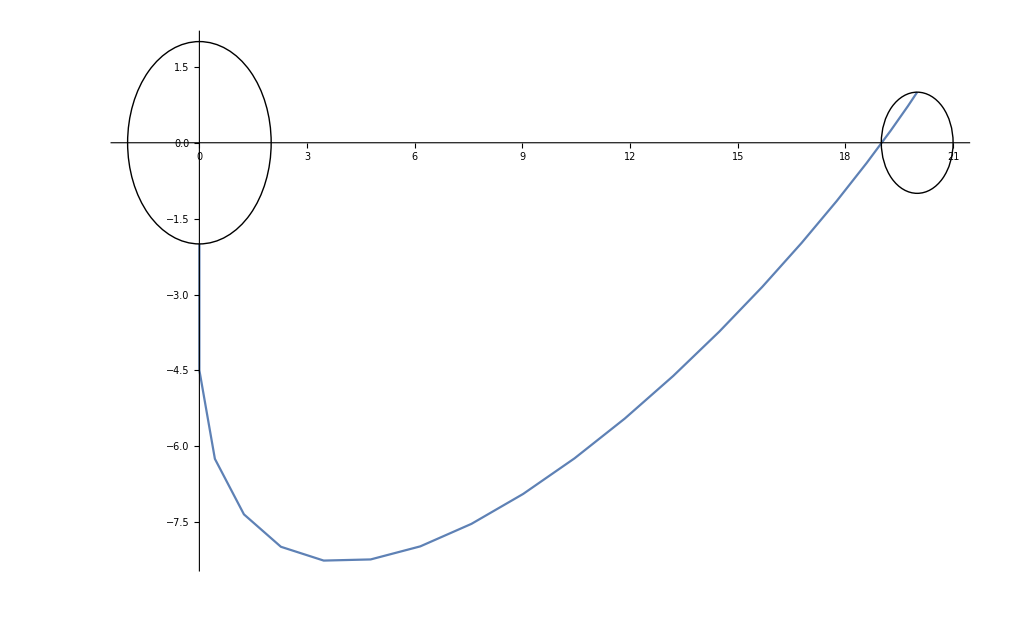

```mathematica
Show[A, B, CC, PlotRange-> All]
```